```mathematica
(1/(50*365))/((1/(50*365))+1/365)
```

1/51

```mathematica
S=(1/R)-(2p/((R-1)+√((R-1)^2+4*R*p)))
```

1/R-(2 p)/(-1+R+√((-1+R)^2+4 p R))

```mathematica
V=(ϵ*(R-1)+ϵ*√((R-1)^2+4*R*p))/(2*R)
```

(1/51 (-1+R)+1/51 √((-1+R)^2+4 p R))/(2 R)

```mathematica
ϵ=1/51
```

1/51

```mathematica
Solve[(1-R S+R V+ϵ)^2-4 (R V+ϵ-R S ϵ)==0,p]
```

{{p→(-63750 R+75088 R^2-8619 R^3-10 √51 √(-2059225 R^2+6805344 R^3-7490925 R^4+2746250 R^5))/(456976 R^2)},{p→(-63750 R+75088 R^2-8619 R^3+10 √51 √(-2059225 R^2+6805344 R^3-7490925 R^4+2746250 R^5))/(456976 R^2)}}

```mathematica
Clear[p]
```

```mathematica
g[R_]:=(-63750 R+75088 R^2-8619 R^3+10 √51 √(-2059225 R^2+6805344 R^3-7490925 R^4+2746250 R^5))/(456976 R^2)
```

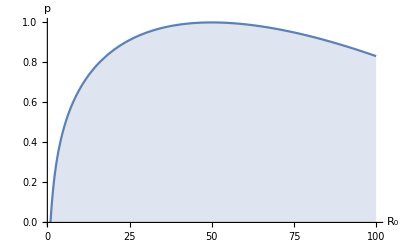

```mathematica
Plot[g[R],{R,0,100},Filling->Bottom,AxesLabel->{Subscript[R, 0],p},PlotRange->All]
```

```mathematica
h[R_]:=g[R+1]
```

LogLinearPlot::invpr: Value of option PlotRange should be positive in the scaled dimensions.

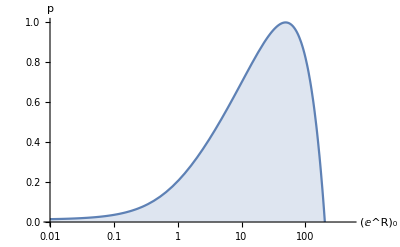

```mathematica
LogLinearPlot[h[R],{R,0.01,500},Filling->Bottom,AxesLabel->{Subscript[R, 0],p},PlotRange->{{0,500},{0,1}}]
```

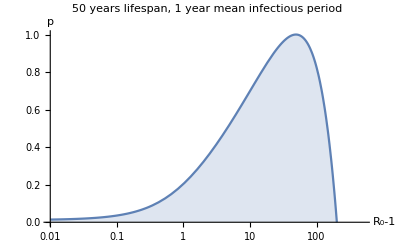

```mathematica
Show[%25,AxesLabel->{HoldForm[Subscript[R, 0]-1],p},PlotLabel->RawBoxes[RowBox[{RowBox[{"50"," ","years"," ","lifespan"}],","," ",RowBox[{"1"," ","year"," ","mean"," ","infectious"," ","period"}]}]],LabelStyle->{GrayLevel[0]}]
```

```mathematica
Export["C:\\Users\\Roger Zhang\\Documents\\GitHub\\RogerZhang\\July_2nd\\Figures\\p_vs_R_0\\50_365.pdf",%26,"PDF"]
```

C:\Users\Roger Zhang\Documents\GitHub\RogerZhang\July_2nd\Figures\p_vs_R_0\50_365.pdf